# INTERNALLY PRESSURISED CYLINDER - von Mises material

```mathematica
Compute2DShape[order_,eltype_]:=Block[{zeta1,zeta2,zeta3,a,b,xi,eta,psis,dpsis},
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,
-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,
(xi+1)(xi-1)(eta+1)(eta-1)};
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];

Pontos e pesos -Gauss Quadrature;
<<NumericalDifferentialEquationAnalysis`
IntegrationRule[porder_,eltype_]:=Block[{pts,w,npts,matpsts},
If[eltype==1,
{pts,w}=Transpose[GaussianQuadratureWeights[porder+1,-1,1]];
npts=Length[pts];
matpsts=Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1];
,
If[porder==1,
matpsts={{1/3,1/3,1/2}};
];
If[porder==2,
matpsts={{1/6,1/6,1/2 1/3},{2/3,1/6,1/2 1/3},{1/6,2/3,1/2 1/3}};
];
];
N[matpsts]
];

Global Assemble;
Assemble[allcoords_,nnodes_,topol_,order_,eltype_,displacement_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob,uglob},

nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=2 Length[nnodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
uglob=Table[Table[{displacement[[2topol[[k,j]] -1]],displacement[[2topol[[k,j]] ]]},{j,1,Length[topol[[k]]]}],{k,1,nels}];

Table[
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiff[order,co,eltype,uglob[[k]]];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[2 i+fu]];
Fglob[[2rowglob]]+=Fe[[2 i]];
,{i,1,rows}];
,{k,1,nels}];

{Kglob,Fglob}
];

Compute a unitary normal vector wrt a circle o radius R;
ComputeNormals[pt_,R_]:=Block[{lines,x,normal,v,delta=10^-9},
rr[x_]=-(x/Sqrt[R^2-(1-delta)x^2]);
pervec[v_]:={-(v[[2]]/Norm[v]),v[[1]]/Norm[v]};
lines=rr[pt[[1]]](x-pt[[1]])+pt[[2]];
normal=({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})/Norm[({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})];
pervec[normal]
];

Compute one dimension shape functions;
ComputeShape[order_,var_,x0_,xf_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf -x0)(i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
Find node ids;
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]];

(*Find node id*)
LineTopology[ids_,order_]:=Block[{k,vg,v,j,i},
k=0;
vg={};
For[j=1,j<Length[ids]/(order),j++,
v={};
For[i=1,i≤order+1,i++,
AppendTo[v,ids[[i+k]]];
];
AppendTo[vg,v];
k+=order;
];
vg
];

Compute the force vector in a circle;
ContributeLineNewmanPressure[nodes_,order_,ids_,R_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,normal,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
normal=ComputeNormals[pt,R];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];
Dirichlet BC;
ContributeLineDirichlet[EK_,EF_,ids_,{dir_,val_}]:=Block[{nodes,i,j,k,Ek=EK,Ef=EF},
nodes=Length[ids];
For[i=1,i≤nodes,i++,

If[dir==1,
Ek[[2ids[[i]]-1,2ids[[i]]-1]]=10^12;
Ef[[2ids[[i]]-1]]=10^12 val;
,
Ek[[2ids[[i]],2ids[[i]]]]=10^12;
Ef[[2ids[[i]]]]=10^12 val;

];

];
{Ek,Ef}
];
Compute the integration point contribution of the integral;
Contribute[data_]:=Block[{psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,B,C,ek,ef,elcoords,weight,stress,Dep,eldisplacement,gradu,epst,epsp,epse,epspeint},

{psis,GradPsi,elcoords,weight,eldisplacement}=data;
{x,y}=psis.elcoords;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;

B={Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]};

(*Displacement gradient*)
gradu=GradPhi.eldisplacement;

(*Infinitesimal Strain Tensor*)
epst=CoumpteStrain[gradu];

(* globalcounter =  integration point index mesh identifier. It has the size of the integration points rule multiplied by the number of mesh elements.*)
(* Plastic strain vector in the last converged step. This vector is updated when the newton method converge.  If[Converge=True, epspsolitern = epspvec] *)
epsp=epspsolitern[[globalcounter]];

(*Integration of the elastoplastic equations*)

{stress,Dep,epse}=ApplyStrainComputeSigmaDep2D[epst,epsp];

epspeint=epst-epse;

(*Store the plastic strain at the current integration point. When newton's method converge the values are transfered to epspsolitern=epspvec. *)
epspvec[[globalcounter]]=epspeint;
globalcounter++;

AppendTo[epsppost,{x,y,epsp}];
AppendTo[stressppost,{x,y,stress}];

(*Element Stiffness Matrix contribution*)
ek=(Transpose[B].Dep.B)weight DetJ;

(*Element Internal force vector contribution*)
ef=(Transpose[B].stress)weight DetJ;

{ek,ef}
];

 Assemble the element stiffness matrix and internal force vectors;
CalcStiff[order_,elcoords_,eltype_,eldisplacement_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w,eldisplacement};
{ek,ef}+=Contribute[data];
,{i,1,npts}
];
{ek,ef}
];

Material point plastic integration;
Fx[{sigxx_, sigyy_ , sigzz_, sigyz_, sigxz_, sigxy_}]:=√(sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))-sig0;
Fprinc[{sig1_,sig2_,sig3_}]:=√(sig1^2+sig2^2-sig2 sig3+sig3^2-sig1 (sig2+sig3))-sig0
ap[{sig1_,sig2_,sig3_}]:={(2 sig1-sig2-sig3)/(2 √(sig1^2+sig2^2-sig2 sig3+sig3^2-sig1 (sig2+sig3))),(-sig1+2 sig2-sig3)/(2 √(sig1^2+sig2^2-sig2 sig3+sig3^2-sig1 (sig2+sig3))),(-sig1-sig2+2 sig3)/(2 √(sig1^2+sig2^2-sig2 sig3+sig3^2-sig1 (sig2+sig3)))}
ax[{sigxx_, sigyy_ , sigzz_, sigyz_, sigxz_, sigxy_}]:={(2 sigxx-sigyy-sigzz)/(2 √(sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))),(-sigxx+2 sigyy-sigzz)/(2 √(sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))),(-sigxx-sigyy+2 sigzz)/(2 √(sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))),(3 sigyz)/(√(sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))),(3 sigxz)/(√(sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))),(3 sigxy)/(√(sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz)))};
dadsigmax[{sigxx_, sigyy_ , sigzz_, sigyz_, sigxz_, sigxy_}]:={{(3 (4 sigxy^2+4 sigxz^2+sigyy^2+4 sigyz^2-2 sigyy sigzz+sigzz^2))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(3 (2 sigxy^2+2 sigxz^2+sigxx sigyy+2 sigyz^2-sigxx sigzz-sigyy sigzz+sigzz^2))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(3 (2 sigxy^2+2 sigxz^2-sigxx sigyy+sigyy^2+2 sigyz^2+sigxx sigzz-sigyy sigzz))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigyz (-2 sigxx+sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxz (-2 sigxx+sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxy (-2 sigxx+sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2))},{-(3 (2 sigxy^2+2 sigxz^2+sigxx sigyy+2 sigyz^2-sigxx sigzz-sigyy sigzz+sigzz^2))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 (sigxx^2+4 sigxy^2+4 sigxz^2+4 sigyz^2-2 sigxx sigzz+sigzz^2))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(3 (sigxx^2+2 sigxy^2+2 sigxz^2+2 sigyz^2+sigyy sigzz-sigxx (sigyy+sigzz)))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigyz (sigxx-2 sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxz (sigxx-2 sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxy (sigxx-2 sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2))},{-(3 (2 sigxy^2+2 sigxz^2-sigxx sigyy+sigyy^2+2 sigyz^2+sigxx sigzz-sigyy sigzz))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(3 (sigxx^2+2 sigxy^2+2 sigxz^2+2 sigyz^2+sigyy sigzz-sigxx (sigyy+sigzz)))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 (sigxx^2+4 sigxy^2+4 sigxz^2-2 sigxx sigyy+sigyy^2+4 sigyz^2))/(4 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigyz (sigxx+sigyy-2 sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxz (sigxx+sigyy-2 sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxy (sigxx+sigyy-2 sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2))},{(3 sigyz (-2 sigxx+sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigyz (sigxx-2 sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigyz (sigxx+sigyy-2 sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz)))/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(9 sigxz sigyz)/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(9 sigxy sigyz)/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2))},{(3 sigxz (-2 sigxx+sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxz (sigxx-2 sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxz (sigxx+sigyy-2 sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(9 sigxz sigyz)/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 (sigxx^2+3 sigxy^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz)))/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(9 sigxy sigxz)/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2))},{(3 sigxy (-2 sigxx+sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxy (sigxx-2 sigyy+sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 sigxy (sigxx+sigyy-2 sigzz))/(2 (sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(9 sigxy sigyz)/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),-(9 sigxy sigxz)/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2)),(3 (sigxx^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz)))/((sigxx^2+3 sigxy^2+3 sigxz^2+sigyy^2+3 sigyz^2-sigyy sigzz+sigzz^2-sigxx (sigyy+sigzz))^(3/2))}}
ProjPrincipal[principalstress_]:=Block[{s1,s2,s3,gamma,xi,guess,,index,flag,R2,asol,strialstar,R,I1,beta,rho,distsqr,sol,projsigstar,invR,projsig,sqrtJ2,newstress,sstarsurface,diff,DHW,G=young/(2(1+nu)),K=young/(3(1-2nu)),Ndir,epse,dlambda,Q,Ctc,trialstress},
(*DHW={{K+4G/3,K-2G/3,K-2G/3},{K-2G/3,K+4G/3,K-2G/3},{K-2G/3,K-2G/3,K+4G/3}};*)
trialstress=principalstress;
s1=trialstress[[1]]-1/3Tr[trialstress];
s2=trialstress[[2]]-1/3Tr[trialstress];
s3=trialstress[[3]]-1/3Tr[trialstress];
(*Print["traial princ = ",trialstress];*)
If[Fprinc[trialstress]>0,
flag=True;
(*beta=ArcTan[-(√((s2-s3)^2) (-2 s1+s2+s3))/((s2-s3) √(s1^2+s2^2-s2 s3+s3^2-s1 (s2+s3))),(√3 √((s2-s3)^2))/(√(s1^2+s2^2-s2 s3+s3^2-s1 (s2+s3)))];*)
beta=-ArcTan[(√3 (s2-s3))/(-2 s1+s2+s3)];
xi=Tr[trialstress]/Sqrt[3];
projsig={xi/Sqrt[3]+2/3 sig0 Cos[beta],xi/Sqrt[3]+2/3 sig0 Cos[beta-2Pi/3],xi/Sqrt[3] +2/3 sig0  Cos[beta+2Pi/3]};
,
flag=False;
projsig=trialstress;
(*epse=Inverse[DHW].trialstress;*)
];
{projsig,flag}
]

EigenSystem[m_]:=Block[{epstprincipalvals,epstprincipaldir,orderedvalues,index,oderedvectors},
{epstprincipalvals,epstprincipaldir}=Eigensystem[m];
orderedvalues=Sort[epstprincipalvals,Greater];
index=Table[Position[epstprincipalvals,orderedvalues[[i]]],{i,1,3}]//Flatten;
oderedvectors=Table[epstprincipaldir[[index[[i]]]],{i,1,3}];
{orderedvalues,oderedvectors}
]
FromVoigtToCart[sig_]:={{sig[[1]],sig[[6]],sig[[5]]},{sig[[6]],sig[[2]],sig[[4]]},{sig[[5]],sig[[4]],sig[[3]]}}
FromCartToVoigt[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],sig[[2,3]],sig[[1,3]],sig[[1,2]]}
ApplyStrainComputeSigmaDep3D[epst_,epsp_]:=Block[{sx,sy,tauxy,sz,ex,ey,exy,sigproj2D,Dep2D,epse2D,Dep,qtrial,gamma,epsetrial,flag,fulltrialstress,dadsigg,sigprojfull,projepse,epsefull,sigsol,R,asol,epse,dlambda,Q,invQ,Ctc,Ce,projsig,projsigstar,internalstress,sstarsurface,epstprincipalvals,epstprincipaldir,epspprincipalvals,epspprincipaldir,fullepst,fullepsp,sigtrprincipalvals,sigtrprincipaldir,sigtrialvoigth,sigprojvoigth,Ce2,G=young/(2(1+nu)),K=young/(3(1-2nu))},
Ce=({{(4 G)/3+K, -(2 G)/3+K, -(2 G)/3+K, 0, 0, 0}, {-(2 G)/3+K, (4 G)/3+K, -(2 G)/3+K, 0, 0, 0}, {-(2 G)/3+K, -(2 G)/3+K, (4 G)/3+K, 0, 0, 0}, {0, 0, 0, G, 0, 0}, {0, 0, 0, 0, G, 0}, {0, 0, 0, 0, 0, G}});

epsetrial=(epst-epsp);
(*Print["epsetrial = ",epsetrial];*)
sigtrialvoigth=Ce.epsetrial;
fullepst=FromVoigtToCart[epst];
fullepsp=FromVoigtToCart[epsp];
fulltrialstress=FromVoigtToCart[sigtrialvoigth];
(*Print["fullepst = ",fullepst];*)

{epstprincipalvals,epstprincipaldir}=EigenSystem[fullepst//N];
(*Print["epstprincipalvals = ",epstprincipalvals];*)
{epspprincipalvals,epspprincipaldir}=EigenSystem[fullepsp//N];
{sigtrprincipalvals,sigtrprincipaldir}=EigenSystem[fulltrialstress//N];
(*Print["sigtrprincipalvals = ",sigtrprincipalvals];*)

{projsig,flag}=ProjPrincipal[sigtrprincipalvals];

sigprojfull=Sum[projsig[[i]]Outer[Times,sigtrprincipaldir[[i]],sigtrprincipaldir[[i]]],{i,1,3}];

sigprojvoigth=FromCartToVoigt[sigprojfull];

epse=Inverse[Ce].sigprojvoigth;
(*Print["sigprojvoigth = ", sigprojvoigth];
Print["Ce = ", Ce//MatrixForm];
Print["epse = ", epse];*)
If[flag==True,
asol=ax[sigprojvoigth];
dadsigg=dadsigmax[sigprojvoigth];
(*gamma=Norm[Inverse[Ce].sigprojvoigth-epst]/Norm[asol];
gamma=Norm[epst-epse]/Norm[asol];*)
gamma=Norm[epsetrial-epse]/Norm[asol];
Q=(IdentityMatrix[6]+gamma Ce.dadsigg);
invQ=Inverse[Q];
R=invQ.Ce;
Dep= R-1/(asol.R.asol) Outer[Times,R.asol,R.asol];
(*Print["Dep = ",Dep//MatrixForm];*)
,
epse=epst-epst;
sigprojvoigth=sigtrialvoigth;
Dep=Ce;
];
(*Dep=Ce;*)
Dep2D={{Dep[[1,1]],Dep[[1,2]],Dep[[1,6]]},{Dep[[2,1]],Dep[[2,2]],Dep[[2,6]]},{Dep[[6,1]],Dep[[6,2]],Dep[[6,6]]}};
(*Print["Dep2D = ",Dep2D//MatrixForm];*)
sigproj2D={sigprojvoigth[[1]],sigprojvoigth[[2]],sigprojvoigth[[6]]};
sx=sigprojvoigth[[1]];
sy=sigprojvoigth[[2]];
tauxy=sigprojvoigth[[6]];
sz=nu(sx+sy);
ex=1/young (sx-nu(sy+sz));
ey=1/young (sy-nu(sx+sz));
exy=tauxy/(G);
epse2D={ex,ey,exy};
{sigproj2D,Dep2D,epse2D}
]
FromVoigtToCart2[sig_]:={{sig[[1]],sig[[3]],0},{sig[[3]],sig[[2]],0},{0,0,0}};
FromCartToVoigt2[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],sig[[2,3]],sig[[1,3]],sig[[1,2]]};
ApplyStrainComputeSigmaDep2D[epst_,epsp_]:=Block[{epstintfull,epspintfull,epspintvoigth,epstintvoigth},
epstintfull=FromVoigtToCart2[epst];
epstintvoigth=FromCartToVoigt2[epstintfull];
epspintfull=FromVoigtToCart2[epsp];
epspintvoigth=FromCartToVoigt2[epspintfull];
ApplyStrainComputeSigmaDep3D[epstintvoigth,epspintvoigth]
];
CoumpteStrain[gradprevsol_]:=Block[{dudx,dudy,dvdx,dvdy,gradu,strain,ex,ey,exy,ux,uy,kk},
(*Print["gradprevsol = ",gradprevsol];*)
{{dudx,dudy},{dvdx,dvdy}}=gradprevsol;
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
{ex,ey,exy}
]
GenerateGridMesh[R0_,RE_,nx_,ny_,order_]:=Block[{x=0.,y=0.,dx,dy,meshnodes,i,j,meshtopology={},allcoords,k,l},
meshnodes={};
k=0;

(*meshnodes=Flatten[Table[Table[{R Cos[θ],R Sin[θ]},{R,R0,RE,(RE-R0)/(nx order-2)}],{θ,0,Pi/2,Pi/2 /(ny order-2)}],1]//N;*)
r=(RE/R0)^(1/(-2+nx order));
meshnodes=Flatten[Table[Table[{ R0 r^(n-1) Cos[θ], R0 r^(n-1) Sin[θ]},{n,1.,nx order-1}],{θ,0,Pi/2,Pi/2 /(ny order-2)}],1]//N;
k=0;
For[i=1 ,i<ny,i++,
l=1;
For[j=1,j<nx,j++,
(*AppendTo[meshtopology,{j+k,j+2+k,4 nx+j+k,4 nx-2+j+k,j+1+k,j+1+nx 2+k,j+nx 4-1+k,2 nx+ j-1+k,2 nx+ j+k}];*)
AppendTo[meshtopology,{l+k,l+2+k,4 nx+l+k,4 nx-2+l+k,l+1+k,l+1+nx 2+k,l+nx 4-1+k,2 nx+ l-1+k,2 nx+l+k}];
l+=2;
];
k+=4 nx-2;
];
If[order==2,
allcoords=Table[meshnodes[[meshtopology[[i,j]]]],{i,1,Length[meshtopology]},{j,1,9}];
,
allcoords=Table[meshnodes[[meshtopology[[i,j]]]],{i,1,Length[meshtopology]},{j,1,4}];
];
{allcoords,meshnodes,meshtopology}
]
GenerateGraphics[nodes_,topology_,order_]:=Block[{meshvis,nodevis},
If[order==2,
meshvis=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nodes,Polygon[topology[[All,{1,5,2,6,3,7,4,8}]]]]}];
,
meshvis=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nodes,Polygon[topology[[All,{1,2,3,4}]]]]}];
];
nodevis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nodes],{Blue,Point[nodes]}}];
{meshvis,nodevis}
];

FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]];

ComputeSol[topol_,coords_,order_,coefs_,eltype_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
Table[
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
,{j,1,kk}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.GradPsi;
Table[
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] );
sol[[i,2]]+=(psis[[j]] coefs[[2id]] );
(*dudx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*dvdx*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*dudy*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*dvdy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );

,
{j,1,kk}];
X[[i,1]]=x;
X[[i,2]]=y;
,{i,1,nels}];
{sol,dsol,X}
]
postproc[X_,sols_]:=Block[{refine,sollists,v,x,y,postvar,sollist},
sollists={};
If[eltype==1,
refine=0.25;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
,
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,1-xi,0,-refine}];
];
sollists=Table[0,{Length[X]}];
pt[xii_,etaa_,var_]:=var/.{xi->xii,eta->etaa};
Sol[xii_,etaa_,var_]:=var/.{xi->xii,eta->etaa};
Table[
x=pt[#1,#2,X[[i]]]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
postvar=Sol[#1,#2,sols[[i]]]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=Table[{x[[1,k]],x[[2,k]],postvar[[k]]},{k,1,Length[postvar]}];
sollists[[i]]=sollist;
,{i,1,Length[X]}];
sollists
]
(*Calcula as tensões nos elementos*)

ComputeStress[dsol_,young_,nu_]:=Block[{I1,stressz,sigxy,sigx,sigy,sigz,strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C,J2,sig,SZ=szz},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
J2=Table[0,{Length[dsol]}];
I1=Table[0,{Length[dsol]}];
stressz=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};

C=young/((1+nu)(1-2nu) ){{1-nu,nu,0},{nu,1-nu,0},{0,0,(1-2nu)/2}};
(*sz[sx_,sy_]:=nu((sx+sy)- (Sh+Sh))+SZ ;*)
stress[[i]]=C.strain;
sig=C.strain;
sigxy=sig[[3]];
sigx=sig[[1]];
sigy=sig[[2]];
sigz=nu(sigx+sigy);
stressz[[i]]=sigz;
I1[[i]]=sigx+sigy+sigz;
J2[[i]]=1/3.(sigx^2+3. sigxy^2+sigy^2-sigy sigz+sigz^2-sigx (sigy+sigz));

];
{stress,strain,stressz,J2,I1}
];
interpolatingQuadBezierCurve[pts_List]/;Length[pts]==3:=BezierCurve[{pts[[1]],1/2 (-pts[[1]]+4 pts[[2]]-pts[[3]]),pts[[3]]}];
interpolatingQuadBezierCurve[ptslist_List]:=interpolatingQuadBezierCurve/@ptslist;
interpolatingQuadBezierCurveComplex[coords_,indices_]:=interpolatingQuadBezierCurve[Map[coords[[#]]&,indices]]
GenerateGraphics[nodes_,topology_]:=Block[{meshvis,nodevis},
nodevis=Graphics[{MapIndexed[Style[Text[#2[[1]],#1,{-1.8,1.8}],FontSize->12]&,nodes],{PointSize[Large],Black,Point[nodes]}}];
Show[nodevis]]
DefineLinePath[pt0_,ptf_,n_]:=Block[{dy,cx0,cy0,cxf,cyf,R,RF,cx,cy,linecoords,deltax,deltay},

{cx0,cy0}=pt0;
{cxf,cyf}=ptf;

RF=Sqrt[cxf^2 + cyf^2];
R=Sqrt[cx0^2 + cy0^2];
Print[RF];
cx=cx0;
cy=cy0;

deltax=(cxf-cx0)/n;
deltay=(cyf-cy0)/n;
linecoords={};
Table[
AppendTo[linecoords,{cx,cy}];
cx+=deltax;
cy+=deltay;
,{i,1,n+1}];
linecoords
];
```

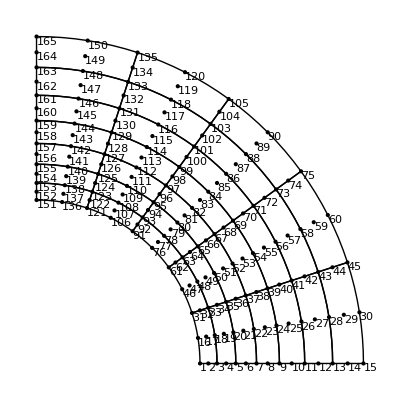

```mathematica
order=2;
serendipity=False;
{allcoords,nnodes,topol}=GenerateGridMesh[100,200,8,6,order];
linestopology=Flatten[Table[
{{topol[[i]][[1]],topol[[i]][[5]],topol[[i]][[2]]},
{topol[[i]][[2]],topol[[i]][[6]],topol[[i]][[3]]},
{topol[[i]][[3]],topol[[i]][[7]],topol[[i]][[4]]},
{topol[[i]][[4]],topol[[i]][[8]],topol[[i]][[1]]}
},{i,1,Length[topol]}],1];
Show[GenerateGraphics[nnodes,topol],Graphics[interpolatingQuadBezierCurveComplex[nnodes,linestopology]],ImageSize->Automatic]
meshvis=Graphics[{Dashed,Black,interpolatingQuadBezierCurveComplex[nnodes,linestopology]}];
x0=100;xf=200.;
y0=0;yf=0;
ndivs=100;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=100;yf=200;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
theta0=0;
thetaf=Pi/2;
r=100.;
searchpathinteriorhole=Table[{r Cos[theta],r Sin[theta]},{theta,theta0,thetaf,(thetaf-theta0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline];
idsleft=FindIds[nnodes,searchpathleftline];
idshole=FindIds[nnodes,searchpathinteriorhole];
```

```mathematica
planestress=False;
ff=0.19209;

f[x_]:=ff;
fac={0.1/0.19209,0.14/0.19209,0.18/0.19209,0.19/0.19209,0.19209/0.19209}
FEXT=ContributeLineNewmanPressure[nnodes,order,idshole,r,f];
eltype=1;
order=2;
young=210;
sig0=0.240;
nu=0.3;
globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];
converge1={};
converge2={};
epspsolu={};
stresssolu={};
sol={};
solss={};
sol2={{0,0}};
sol3={};
steps=10;
factor=1/steps;
displace=Table[0,{Length[nnodes] 2}];
(*AppendTo[sol,displace];*)

For[i=1,i≤Length[fac],i++,
diverge=False;
convergevec1={};
convergevec2={};
Print["i = ",i, " | fac = ",fac[[i]], " | diverge = ",diverge];
counter=1;
err1=10;
err2=10;
temp=100;
tol=10^-9;
dw=Table[0,{Length[nnodes] 2}];
While[counter≤20&& err1>tol,

epsppost={};
stressppost={};
globalcounter=1;
{KT,FINT}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
imposex=1;
imposey=2;

R=fac[[i]] FEXT-FINT;
{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
dw=LinearSolve[KT,R,Method->"Multifrontal"];
(*dw=LinearSolve[KT,R];*)
res=Norm[dw];
displace+=dw;
err1=Norm[R]/Norm[fac[[i]] FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dw]/Norm[displace];
AppendTo[convergevec1,{counter,err2}];
AppendTo[convergevec2,{counter,err1}];
Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[factor FEXT], "  |Δu|/|u| = ",Norm[dw]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dw]];
counter++;
];

AppendTo[stresssolu,stressppost];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];

AppendTo[converge1,convergevec1];
AppendTo[converge2,convergevec2];
AppendTo[sol,displace];
AppendTo[sol2,{displace[[FindIds[nnodes,{{200,0}}][[1]] 2-1]], ff fac[[i]]}];
AppendTo[sol3,epspvec];
factor+=1/steps;
(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
];
```

{0.520589,0.728825,0.937061,0.98912,1.}

i = 1 | fac = 0.520589 | diverge = False

Iteration number = 1  |R|/|FE| =  5.20589  |Δu|/|u| = 1.  |R| =  5.17804 |dw| = 0.928717

Iteration number = 2  |R|/|FE| =  3.50155×10^-13  |Δu|/|u| = 6.405×10^-15  |R| =  3.48282×10^-13 |dw| = 5.94843×10^-15

i = 2 | fac = 0.728825 | diverge = False

Iteration number = 1  |R|/|FE| =  1.04118  |Δu|/|u| = 0.285714  |R| =  2.07121 |dw| = 0.371487

Iteration number = 2  |R|/|FE| =  1.26315  |Δu|/|u| = 0.0752628  |R| =  2.51279 |dw| = 0.105795

Iteration number = 3  |R|/|FE| =  0.0343336  |Δu|/|u| = 0.000862015  |R| =  0.0682998 |dw| = 0.00121274

Iteration number = 4  |R|/|FE| =  0.0000143861  |Δu|/|u| = 3.25627×10^-7  |R| =  0.0000286182 |dw| = 4.58113×10^-7

Iteration number = 5  |R|/|FE| =  2.45422×10^-12  |Δu|/|u| = 5.29188×10^-14  |R| =  4.88217×10^-12 |dw| = 7.44495×10^-14

i = 3 | fac = 0.937061 | diverge = False

Iteration number = 1  |R|/|FE| =  0.694128  |Δu|/|u| = 0.323927  |R| =  2.07124 |dw| = 0.673947

Iteration number = 2  |R|/|FE| =  1.18937  |Δu|/|u| = 0.144389  |R| =  3.54903 |dw| = 0.350909

Iteration number = 3  |R|/|FE| =  0.496386  |Δu|/|u| = 0.0466375  |R| =  1.48119 |dw| = 0.118874

Iteration number = 4  |R|/|FE| =  0.00927106  |Δu|/|u| = 0.000374507  |R| =  0.0276644 |dw| = 0.000954932

Iteration number = 5  |R|/|FE| =  1.83631×10^-6  |Δu|/|u| = 7.96906×10^-8  |R| =  5.47944×10^-6 |dw| = 2.03198×10^-7

Iteration number = 6  |R|/|FE| =  1.33683×10^-13  |Δu|/|u| = 8.40309×10^-15  |R| =  3.98903×10^-13 |dw| = 2.14265×10^-14

i = 4 | fac = 0.98912 | diverge = False

Iteration number = 1  |R|/|FE| =  0.133186  |Δu|/|u| = 0.171012  |R| =  0.529895 |dw| = 0.525927

Iteration number = 2  |R|/|FE| =  0.48936  |Δu|/|u| = 0.0889161  |R| =  1.94697 |dw| = 0.300108

Iteration number = 3  |R|/|FE| =  0.155136  |Δu|/|u| = 0.0269202  |R| =  0.617225 |dw| = 0.0933725

Iteration number = 4  |R|/|FE| =  0.00197242  |Δu|/|u| = 0.000186993  |R| =  0.00784748 |dw| = 0.000648704

Iteration number = 5  |R|/|FE| =  2.01525×10^-7  |Δu|/|u| = 2.00223×10^-8  |R| =  8.01785×10^-7 |dw| = 6.94602×10^-8

Iteration number = 6  |R|/|FE| =  9.58136×10^-14  |Δu|/|u| = 1.71403×10^-14  |R| =  3.81204×10^-13 |dw| = 5.94622×10^-14

i = 5 | fac = 1. | diverge = False

Iteration number = 1  |R|/|FE| =  0.0264626  |Δu|/|u| = 0.106896  |R| =  0.131605 |dw| = 0.415201

Iteration number = 2  |R|/|FE| =  0.110309  |Δu|/|u| = 0.088744  |R| =  0.548591 |dw| = 0.378252

Iteration number = 3  |R|/|FE| =  0.218737  |Δu|/|u| = 0.245192  |R| =  1.08783 |dw| = 1.38446

Iteration number = 4  |R|/|FE| =  0.0626498  |Δu|/|u| = 0.196897  |R| =  0.311573 |dw| = 1.38428

Iteration number = 5  |R|/|FE| =  0.0219568  |Δu|/|u| = 0.116204  |R| =  0.109196 |dw| = 0.924373

Iteration number = 6  |R|/|FE| =  0.00506078  |Δu|/|u| = 0.0321215  |R| =  0.0251685 |dw| = 0.263996

Iteration number = 7  |R|/|FE| =  0.000301764  |Δu|/|u| = 0.00192191  |R| =  0.00150075 |dw| = 0.015826

Iteration number = 8  |R|/|FE| =  1.00927×10^-6  |Δu|/|u| = 6.30945×10^-6  |R| =  5.01936×10^-6 |dw| = 0.0000519555

Iteration number = 9  |R|/|FE| =  1.08346×10^-11  |Δu|/|u| = 6.77325×10^-11  |R| =  5.38833×10^-11 |dw| = 5.57746×10^-10

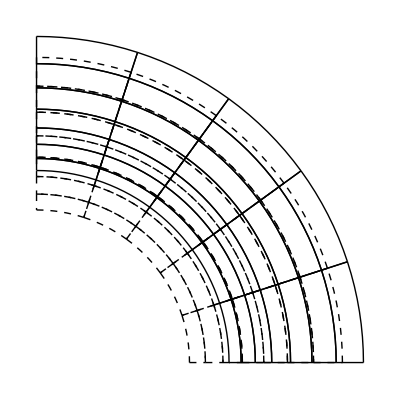

```mathematica
sol1=solss[[5]];
scale=30;
deformed=(Flatten[nnodes]+scale sol1);
tabdeformed=Table[{deformed[[i]],deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{Thick,Black,interpolatingQuadBezierCurveComplex[tabdeformed,linestopology]}];
Show[meshVisDef,meshvis]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

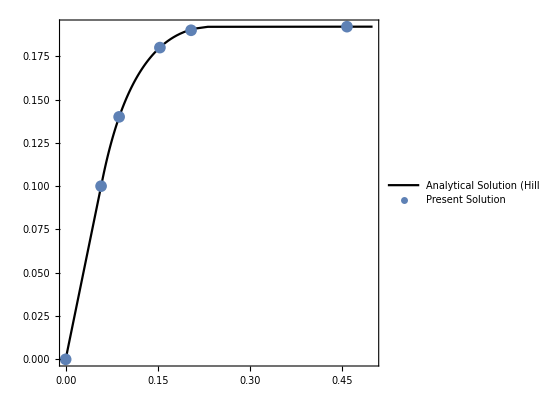

```mathematica
data=Table[i,{i,0,0.192,0.001}];
Clear[f]
eq[P_]:=(Log[c/a]+0.5 (1-c^2/b^2))-P/Y;
ub0[P_]:=2 P b/(young (b^2/a^2-1))(1-nu^2);
ub1[c_]:=Y c^2 (1-nu^2)/(young b);
Clear[a,b,c,nu,sigy,young]
subst={Y->2 sigy/Sqrt[3],young->210, b->200,a->100,sigy->0.240,nu->0.3};
P0=Y/2 (1 - a^2 /b^2) //.subst;
f[P_]:=Block[{},
eqc=eq[P]//.subst;
solc=FindRoot[eqc,{c,0.2}][[1,2]];
solu=ub1[solc]//.subst;
solu
]
computec[P_]:=Block[{},
eqc=eq[P]//.subst;
solc=FindRoot[eqc,{c,100}][[1,2]]
]
ComputeAnalyticalStress[r_,P_]:=Block[{a=100,b=200,sigy=0.24,sigr,sigt,cc,Y},
Y=2 sigy/Sqrt[3];
cc=computec[P];
If[a<=r<=cc,
sigr=Y(-0.5 -Log[cc/r]+cc^2 /(2 b^2));
sigt=Y(0.5 -Log[cc/r]+cc^2 /(2 b^2));
];
If[cc<=r≤b,
sigr=-Y cc^2 /(2 b^2)(b^2 / r^2 -1);
sigt=Y cc^2 /(2 b^2)(b^2 / r^2 +1);
];
{sigr,sigt}
]
u[P_]:=If[P<P0,ub0[P],f[P]]
tab=Table[{u[data[[i]]]//.subst ,data[[i]]},{i,1,Length[data]}];
AppendTo[tab,{0.5,0.19208}];
lp=ListLinePlot[tab,PlotStyle->{Black},Frame->True,PlotLegends->{"Analytical Solution (Hill - 1950)"}];
Show[lp,ListPlot[sol2,PlotRange->All,PlotMarkers->{Automatic,12},Frame->True,FrameLabel->{"radial displacement at outer face (mm)","Pressure (MPa)"},PlotLegends->{"Present Solution"}],PlotRange->All,AspectRatio->1,ImageSize->400]
```

```mathematica
Clear[r]
tabsr1=Table[{r,ComputeAnalyticalStress[r,0.18][[1]]},{r,100,200,0.5}];
tabst1=Table[{r,ComputeAnalyticalStress[r,0.18][[2]]},{r,100,200,0.5}];
tabsr2=Table[{r,ComputeAnalyticalStress[r,0.1][[1]]},{r,100,200,0.5}];
tabst2=Table[{r,ComputeAnalyticalStress[r,0.1][[2]]},{r,100,200,0.5}];
lpa1=ListLinePlot[{tabsr1,tabsr2},Frame->True,AspectRatio->1.,PlotStyle->{Red,Black},PlotLegends->{" (Hill - 1950) radial stress P = 0.10 GPa "," (Hill - 1950)  radial stress P = 0.18 GPa"}];
lpa2=ListLinePlot[{tabst1,tabst2},Frame->True,AspectRatio->1.,PlotStyle->{Red,Black},PlotLegends->{" (Hill - 1950) tangencial stress P = 0.10 GPa "," (Hill - 1950) tangencial stress P = 0.18 GPa"}];
```

200

200

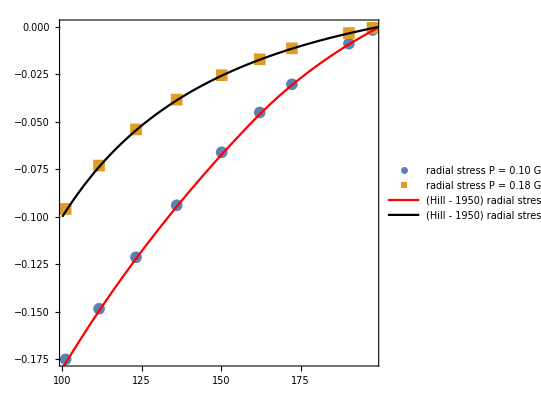

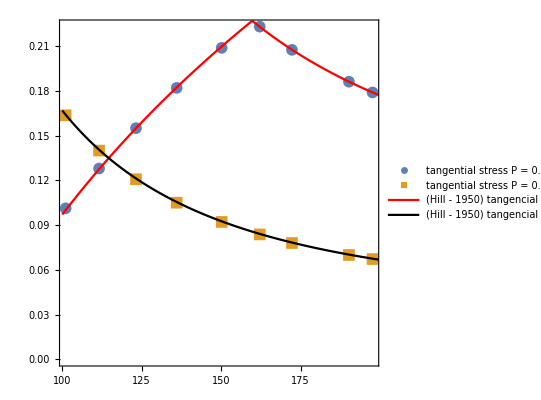

```mathematica
step=3;
path=DefineLinePath[{100,0},{200 ,0},8];
intpoint=1;
x=1;
y=2;
sx=1;
sy=2;
stredata=Table[{{stresssolu[[step]][[i]][[1]],stresssolu[[step]][[i]][[2]]},stresssolu[[step]][[i]][[3]]},{i,1,Length[stresssolu[[step]]]}];
datac=Flatten[Nearest[Transpose[stredata][[1]],path],1];
idss=Flatten[Position[Transpose[stredata][[1]],Alternatives@@datac]];
ssx1=Table[{stredata[[idss[[i]]]][[1]][[1]],stredata[[idss[[i]]]][[2]][[sx]]},{i,1,Length[idss]}];
ssy1=Table[{stredata[[idss[[i]]]][[1]][[1]],stredata[[idss[[i]]]][[2]][[sy]]},{i,1,Length[idss]}];

step=1;
path=DefineLinePath[{100,0},{200 ,0},8];
intpoint=1;
x=1;
y=2;
sx=1;
sy=2;
stredata=Table[{{stresssolu[[step]][[i]][[1]],stresssolu[[step]][[i]][[2]]},stresssolu[[step]][[i]][[3]]},{i,1,Length[stresssolu[[step]]]}];
datac=Flatten[Nearest[Transpose[stredata][[1]],path],1];
idss=Flatten[Position[Transpose[stredata][[1]],Alternatives@@datac]];
ssx2=Table[{stredata[[idss[[i]]]][[1]][[1]],stredata[[idss[[i]]]][[2]][[sx]]},{i,1,Length[idss]}];
ssy2=Table[{stredata[[idss[[i]]]][[1]][[1]],stredata[[idss[[i]]]][[2]][[sy]]},{i,1,Length[idss]}];
Show[ListPlot[{ssx1,ssx2},Frame->True,AspectRatio->1.,PlotMarkers->{Automatic, 12},PlotLegends->{"radial stress P = 0.10 GPa","radial stress P = 0.18 GPa"}],lpa1]
Show[ListPlot[{ssy1,ssy2},Frame->True,AspectRatio->1.,PlotMarkers->{Automatic, 12},PlotLegends->{"tangential stress P = 0.10 GPa","tangential stress P = 0.18 GPa"}],lpa2]
```

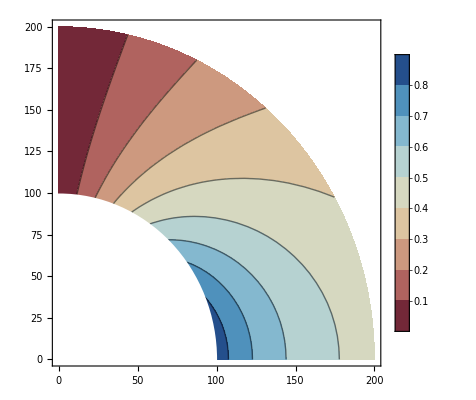

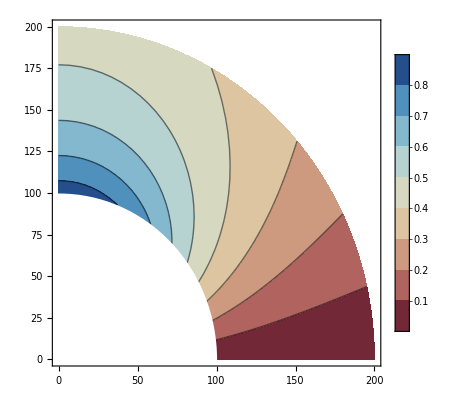

```mathematica
RR=100;
sol=solss[[5]];
young=210;
nu=0.3;
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
{stress,strain,stressz,J2,I1}=ComputeStress[dsols,young,nu];
(*tabux=computesollist[X,sols,1];*)
tabux=postproc[X,Transpose[sols][[1]]];
(*tabuy=computesollist[X,sols,2];*)
tabuy=postproc[X,Transpose[sols][[2]]];
(*tabsx=computesollist[X,stress,1];*)
tabsx=postproc[X,Transpose[stress][[1]]];
(*tabsy=computesollist[X,stress,2];*)
tabsy=postproc[X,Transpose[stress][[2]]];
(*tabsxy=computesollist[X,stress,3];*)
tabsxy=postproc[X,Transpose[stress][[3]]];
(*tabsJ2=computesollist2[X,J2,3];*)
tabsJ2=postproc[X,J2];
tabsI1=postproc[X,I1];
tabssz=postproc[X,stressz];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},RR]},AspectRatio->Automatic]];
n=Automatic;
lpux=ListContourPlot[Flatten[tabux,1],ColorFunction->"RedBlueTones",AspectRatio->Automatic,PlotLegends->Automatic];
lpuy=ListContourPlot[Flatten[tabuy,1],ColorFunction->"RedBlueTones",AspectRatio->Automatic,PlotLegends->Automatic];
Show[lpux,lpd]
Show[lpuy,lpd]
```